## Code for S.U. Shringarpure & J.D. Franson, Proposal for a destructive controlled phase gate using linear optics. Sci Rep 11, 22067 (2021).

# Ideal detectors

## Destructive C-Phase Gate

-Graphics-

## Working Constraints: 2 t_1 t_2 t_3=1 and r_2=r_1 t_2

### Allowed Solutions:

```mathematica
t1[t3_]=√(2/(4 t3^2+1));
```

```mathematica
t2 [t3_]= 1/(√(2-t1[t3]^2));
```

### t_1 and t_2 v. t_3

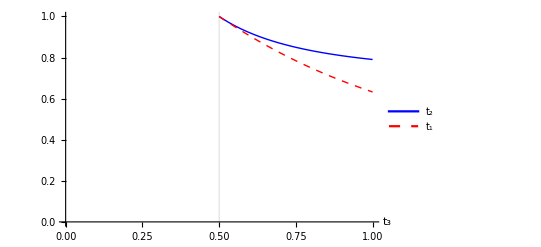

```mathematica
Plot[{t2[t3],t1[t3]},{t3,0,1},PlotRange->{0,1},PlotLegends->Placed[{"t_2","t_1"},{0.25,0.8}],AxesLabel->{"t_3"},LabelStyle->Large,GridLines->{{0.5},None},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},AxesStyle->{{Thick,Black},{Thick,Black}}]
```

### r_2 r_3 v. t_3

```mathematica
FindMaximum[{√((1-t2[t3]^2)(1-t3^2)),0≤ t3≤1},{t3,0.6}]
```

{0.353553,{t3→0.707107}}

```mathematica
{t1[1/(√2)],t2[1/√2]}
```

{√(2/3),(√3)/2}

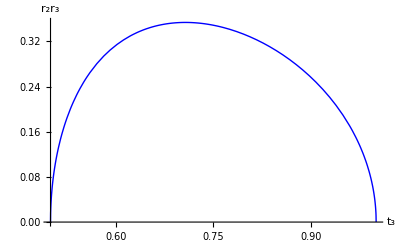

```mathematica
Plot[√((1-t2[t3]^2)(1-t3^2)),{t3,0.5,1},PlotRange->Full,GridLines->{{1/√2},{√((1-t2[1/√2]^2)(1-1/2))}},LabelStyle->Large,AxesLabel->{"t_3","r_2r_3"},AxesStyle-> {{Thick,Black},{Thick,Black}},ImageSize->Scaled[0.5],PlotStyle->{Thick,Blue}]
```

## P_D success probability for π shift Gate

ϕ is the phase of the

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.25(1-t2^2)(1-t3^2)(1+2(α^2-(1-α^2))Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]);
```

```mathematica
Average= (∫_0^1 ∫_0^1 ∫_0^(2π) PD[α,γ,ϕ,√3/2,1/(√2)]ⅆϕⅆγⅆα)/(2π)
```

(∫_0^(2 π) (0.03125-0.00694444 Re[ⅇ^(ⅈ ϕ)])ⅆϕ)/(2 π)

```mathematica
(∫_0^(2 π) (0.03125-0.006944444444444444 Cos[ϕ])ⅆϕ)/(2 π)
```

0.03125

```mathematica
Plot3D[ PD[α,γ,0,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

```mathematica
FindMaximum[{PD[α,γ,0,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1},{α,γ}]
```

{0.0624999,{α→0.999999,γ→0.707106}}

```mathematica
Plot3D[ PD[α,γ,π/2,(√3)/2,1/√2],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

-Graphics3D-

## P_D success probability for π/2 shift Gate

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.18082(1-t2^2)(1-t3^2)(1+2(α^2 Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]+(1-α^2)Re[ⅈ  γ √(1-γ^2)ⅇ^(ⅈ ϕ)]));
```

```mathematica
Average= (∫_0^1 ∫_0^1 ∫_0^(2π) Simplify[PD[α,γ,ϕ,(√3)/2,1/√2]]ⅆϕⅆγⅆα)/(2π)
```

(∫_0^(2 π) (0.0226025-0.0100456 Im[ⅇ^(ⅈ ϕ)]+0.00502278 Re[ⅇ^(ⅈ ϕ)])ⅆϕ)/(2 π)

```mathematica
(∫_0^(2 π) (0.0226025-0.010045555555555556 Sin[ϕ]+0.005022777777777777 Cos[ϕ])ⅆϕ)/(2 π)
```

0.0226025

Average success probability is 0.0226

```mathematica
Plot3D[ PD[α,γ,0,√3/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

```mathematica
Plot3D[ PD[α,γ,π/2,(√3)/2,1/(√2)],{α,0,1},{γ,0,1},LabelStyle->Large,AxesStyle->{{Thick,Black},{Thick,Black},{Thick,Black}}, PlotRange->Automatic,ImageSize->Large,Mesh->None,AxesLabel->{"α","γ","P_D"},ColorFunction->"Rainbow",PlotStyle->Opacity[0.8]]
```

-Graphics3D-

```mathematica
FindMaximum[{PD[α,γ,ϕ,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1&&ϕ≥ 0&&ϕ<2π},{α,γ,ϕ}]
```

{0.0301362,{α→0.999997,γ→0.707105,ϕ→0.00661122}}

```mathematica
FindMaximum[{PD[α,γ,0,(√3)/2,1/(√2)],α≥0&&α≤ 1&&γ≥ 0&&γ≤ 1},{α,γ}]
```

{0.0452049,{α→0.999998,γ→0.707106}}

## KLM C-Phase Gate

Knill, E., Laflamme, R. & Milburn, G. A scheme for efficient quantum computation with linear optics. Nature 409, 46–52 (2001).

## P_KLM success probability for π shift Gate

```mathematica
0.25 0.25 (*Success probabilities of two Nonlinear π/2 Phase gates multiplied*)
```

0.0625

## P_KLM success probability for π/2 shift Gate

```mathematica
0.18082 0.18082 (*Success probabilities of two Nonlinear π/2 Phase gates multiplied*)
```

0.0326959

# Inefficient detectors

## Destructive C-Phase Gate with inefficient detectors

## Main calculations

-Graphics-

```mathematica
B[t_]={{t,ⅈ √(1-t^2)},{ⅈ  √(1-t^2),t}};
Subscript[t, 1]=√(2/3);
Subscript[t, 2]=(√3)/2;
Subscript[t, 3]=1/(√2);
```

### Modes “T” and “a” mix at the first beam splitter:

```mathematica
{Subscript[c, T],Subscript[c, a]}=B[Subscript[t, 1]].{Subscript[c, T1],Subscript[c, a1]};
```

### Nonlinear phase gate

```mathematica
BNSG[θ_,ϕ_]:={{Cos[θ],-ⅇ^(+ⅈ ϕ)Sin[θ]},{+ⅇ^(-ⅈ ϕ)Sin[θ],Cos[θ]}};
θ1=π/8; ϕ1=0;
θ2=65.5302/180 π; ϕ2=0;
θ3=-π/8; ϕ3=0;
ϕ4=π;
```

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{Subscript[c, 21],Subscript[c, 31]}=BNSG[θ1,ϕ1].{Subscript[c, 22],Subscript[c, 32]};
Subscript[c, T1]=ⅇ^(-ⅈ ϕ4)Subscript[c, T2];
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{Subscript[c, T2],Subscript[c, 22]}=BNSG[θ2,ϕ2].{Subscript[c, T3],Subscript[c, 23]};
Subscript[c, 32]=Subscript[c, 33];
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{Subscript[c, 23],Subscript[c, 33]}=BNSG[θ3,ϕ3].{Subscript[c, 24],Subscript[c, 34]};
Subscript[c, T3]=Subscript[c, T4];
```

#### Inefficient detectors

```mathematica
{Subscript[c, 24],Subscript[c, 2vac]}=B[√η].{Subscript[c, 25],Subscript[c, 2d]};
{Subscript[c, 34],Subscript[c, 3vac]}=B[√η].{Subscript[c, 35],Subscript[c, 3d]};
Subscript[c, T4]=Subscript[c, T5];
```

### Modes “T1” and “b” mix at the second beam splitter:

```mathematica
{Subscript[c, T5],Subscript[c, b]}=B[Subscript[t, 2]].{Subscript[c, T6],Subscript[c, b1]};
```

### Modes “T2” and “c” mix at the third beam splitter:

```mathematica
{Subscript[c, T6],Subscript[c, c]}=B[Subscript[t, 3]].{Subscript[c, T7],Subscript[c, c1]};
```

### Inefficient detectors: Modeled as Perfect ones with beam splitter of t=√η

```mathematica
{Subscript[c, a1],Subscript[c, ad1]}=B[√η].{Subscript[c, ap],Subscript[c, ad]};
{Subscript[c, b1],Subscript[c, bd1]}=B[√η].{Subscript[c, bp],Subscript[c, bd]};
{Subscript[c, c1],Subscript[c, cd1]}=B[√η].{Subscript[c, cp],Subscript[c, cd]};
```

## Results

```mathematica
Subscript[ψ, T]=α +β Subscript[c, T];(*Target = α0+β1*)
Subscript[ψ, CA]=γ Subscript[c, b]+δ Subscript[c, a];(*Control = γ01+δ10*)
ψ=Expand[Subscript[ψ, T] Subscript[ψ, CA] Subscript[c, 21]];
creationops=FullSimplify[CoefficientList[CoefficientList[ψ,{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp],Subscript[c, 25],Subscript[c, 35]}][[1,1,2,2,1]],{Subscript[c, 2d],Subscript[c, 3d],Subscript[c, ad],Subscript[c, bd],Subscript[c, cd],Subscript[c, T7]},{3,3,3,3,3,3}]];
fockstate=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationops[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3}];

P=Map[Abs[#]^2&,fockstate,{6}];
```

### Fidelity

```mathematica
F[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
Total[P[[1,1,1,1,1]]]/Total[P,6]
];
AvF[η_]:=N[1/(2π)^2 NIntegrate[F[η,α,γ,ϕT,ϕC],{α,0,1},{γ,0,1},{ϕT,0,2π},{ϕC,0,2π}]];
```

## KLM C-Phase Gate with inefficient detectors

## Main Calculations

### after 50-50 Beam splitter on the left

```mathematica
{t10,b10}=BNSG[π/4,0].{t11,b11};
```

### Top Nonlinear Sign Gate

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{t21,t31}=BNSG[θ1,ϕ1].{t22,t32};
t11=ⅇ^(-ⅈ ϕ4)t12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{t12,t22}=BNSG[θ2,ϕ2].{t13,t23};
t32=t33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{t23,t33}=BNSG[θ3,ϕ3].{t24,t34};
t13=t14;
```

#### Inefficient detectors

```mathematica
{t24,t2vac}=B[√η].{t25,t2dump};
{t34,t3vac}=B[√η].{t35,t3dump};
t14=t15;
```

### Bottom Nonlinear Sign Gate

#### after Beam splitter 1 ( coupling modes 2 and 3)

```mathematica
{b21,b31}=BNSG[θ1,ϕ1].{b22,b32};
b11=ⅇ^(-ⅈ ϕ4)b12;
```

#### after Beam splitter 2 (coupling modes 1 and 2)

```mathematica
{b12,b22}=BNSG[θ2,ϕ2].{b13,b23};
b32=b33;
```

#### after Beam splitter 3 (coupling modes 2 and 3)

```mathematica
{b23,b33}=BNSG[θ3,ϕ3].{b24,b34};
b13=b14;
```

#### Inefficient detectors

```mathematica
{b24,b2vac}=B[√η].{b25,b2dump};
{b34,b3vac}=B[√η].{b35,b3dump};
b14=b15;
```

### after 50-50 Beam splitter on the right

```mathematica
{t15,b15}=BNSG[-π/4,0].{t16,b16};
```

## Results

```mathematica
creationopsKLM=FullSimplify[CoefficientList[CoefficientList[(α+β t10)(γ+b10 δ)t21 b21,{t35,b35,t25,b25}][[1,1,2,2]],{t2dump,t3dump,b2dump,b3dump,t16,b16},{3,3,3,3,2,2}]];
fockstateKLM=Table[√((i-1)!(j-1)!(k-1)!(l-1)!(m-1)!(n-1)!)creationopsKLM[[i,j,k,l,m,n]],{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,2},{n,1,2}];

PKLM=Map[Abs[#]^2&,fockstate,{6}];
```

#### Fidelity

```mathematica
FKLM[η_,α_,γ_,ϕT_,ϕC_]=Module[{},
β=√(1-α^2)ⅇ^(ⅈ ϕT);
δ=√(1-γ^2)ⅇ^(ⅈ ϕC);
Total[PKLM[[1,1,1,1]],2]/Total[PKLM,6]
];
AvFKLM[η_]:=N[1/(2π)^2 NIntegrate[FKLM[η,α,γ,ϕT,ϕC],{α,0,1},{γ,0,1},{ϕT,0,2π},{ϕC,0,2π}]];
```

## Fidelity Comparisons

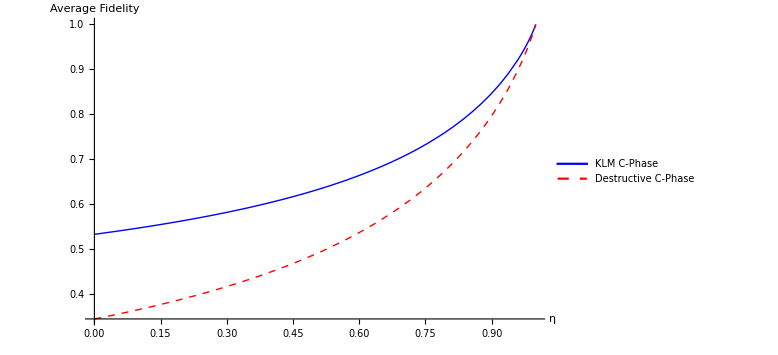

```mathematica
Plot[{AvFKLM[η],AvF[η]},{η,0,1},PlotRange->Full,LabelStyle->Large,AxesLabel->{"η","Average Fidelity"},ImageSize->Large,RotateLabel->True,PlotLegends->Placed[{"KLM C-Phase","Destructive C-Phase"},{0.35,.75}],PlotStyle->{{Thick,Blue},{Thick,Dashed,Red}},AxesStyle->{{Thick,Black},{Thick,Black}}]
```